# QCD-SIGW - simple Mathematica version

Port of the tabulated-kernel part of gfranciolini/QCD-SIGW (core/kernel.py, spectra.py, background_qcd.py). Inputs: data/bg.csv (columns eta, a, calH, w, cs2, grho, gs; no header) and kernels_data_csv/kernel_N.csv (first row = s, first column = t, body = I2bar). Keep this notebook in the folder that contains data/ and kernels_data_csv/.

## 1. Paths and constants

```mathematica
dir = If[$InputFileName =!= "", DirectoryName[$InputFileName], NotebookDirectory[]];
bgPath = FileNameJoin[{dir, "data", "bg.csv"}];
kernelDir = FileNameJoin[{dir, "kernels_data_csv"}];

(* same conventions as core/spectra.py and core/kernel.py *)
mpcInvToHz = 1/6.313*^14;                (* f[Hz] = k[Mpc^-1]/6.313e14 *)
fnHzToK[f_] := f 10.^-9/mpcInvToHz;
etaCFactor = 400.;                        (* eta_c(k) = 400/k *)
tResonance = Sqrt[3.] - 1;
uOf[t_, s_] := (t + s + 1)/2;
vOf[t_, s_] := (t - s + 1)/2;
weight[t_, s_] := (t (2 + t) (s^2 - 1)/((1 - s + t) (1 + s + t)))^2;
```

## 2. Background (bg.csv)

```mathematica
bgRaw = Import[bgPath, "CSV"];
If[! NumberQ[bgRaw[[1, 1]]], bgRaw = Rest[bgRaw]];
If[Length[bgRaw[[1]]] =!= 7, Print["warning: bg.csv should have 7 columns"]];
{etaL, aL, hL, wL, cs2L, grhoL, gsL} = N @ Transpose[bgRaw];
If[! OrderedQ[etaL] || Length[DeleteDuplicates[etaL]] =!= Length[etaL], Print["warning: eta is not strictly increasing"]];
Dimensions[bgRaw]
```

{1054,7}

```mathematica
(* linear interpolation in ln(eta), clamped at the table ends (as _lookup in background_qcd.py) *)
mkItp[y_] := Interpolation[Transpose[{Log[etaL], y}], InterpolationOrder -> 1];
itpLnA = mkItp[Log[aL]]; itpLnH = mkItp[Log[hL]]; itpW = mkItp[wL]; itpCs2 = mkItp[cs2L];
lnEta[eta_] := Clip[Log[eta], {Log[First[etaL]], Log[Last[etaL]]}];
aOfEta[eta_] := Exp[itpLnA[lnEta[eta]]];
hOfEta[eta_] := Exp[itpLnH[lnEta[eta]]];     (* conformal Hubble rate [Mpc^-1] *)
wOfEta[eta_] := itpW[lnEta[eta]];
cs2OfEta[eta_] := itpCs2[lnEta[eta]];
```

## 3. Kernel tables

```mathematica
loadKernel[{file_, f_, k_}] := Module[{raw = Import[FileNameJoin[{kernelDir, file}], "CSV"]},
   <|"f" -> N[f], "k" -> N[k], "s" -> N @ Rest[First[raw]], "t" -> N @ raw[[2 ;;, 1]], "I2" -> N @ raw[[2 ;;, 2 ;;]]|>];
meta = Rest @ Import[FileNameJoin[{kernelDir, "kernels_meta.csv"}], "CSV"];   (* file, f_nHz, k *)
kernels = loadKernel /@ meta;
fList = #["f"] & /@ kernels;
{Length[kernels], Dimensions[kernels[[1]]["I2"]]}
```

{110,{1442,24}}

## 4. Spectra (spectra.py)

```mathematica
trapz[x_, y_] := Total[Differences[x] (Most[y] + Rest[y])/2];

flatPz[k_] := 1.;
lognormalPz[kstar_, sigma_][k_] := Exp[-(Log10[k/kstar])^2/(2 sigma^2)]/Sqrt[2 Pi sigma^2];

(* x_c^2 <P_h>/A^2 = 4 Int dt Int ds W(t,s) I2bar(t,s) Pz(k u) Pz(k v), trapezoid on the table grid *)
phKernel[ker_, pz_] := Module[{t = ker["t"], s = ker["s"], k = ker["k"], tt, ss, w},
   tt = Outer[#1 &, t, s]; ss = Outer[#2 &, t, s];
   w = weight[tt, ss] pz[k uOf[tt, ss]] pz[k vOf[tt, ss]] ker["I2"];
   4 trapz[t, trapz[s, #] & /@ w]];

(* Omega_GW h^2/(Omega_r0 h^2 A^2) = c_g/24 Ph/(calH_c eta_c)^2,  c_g = (a_c H_c/(a_f H_f))^2 *)
omegaGW[k_, ph_, etaF_: 0.5] := Module[{etaC = etaCFactor/k, hc, ac, hf, af, cg},
   hc = hOfEta[etaC]; ac = aOfEta[etaC]; hf = hOfEta[etaF]; af = aOfEta[etaF];
   cg = (ac hc/(af hf))^2;
   cg/24 ph/(hc etaC)^2];
```

## 5. Log-normal and flat spectra

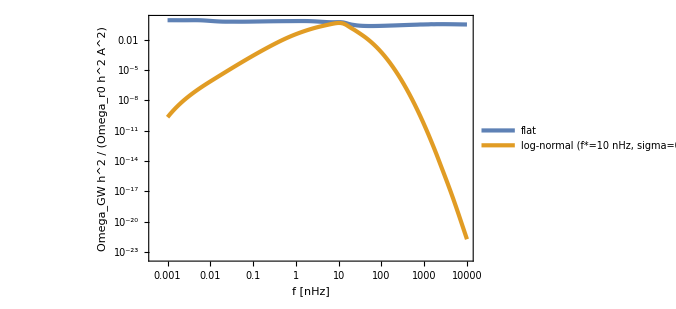

```mathematica
logFstar = 1.; sigma0 = 0.4;     (* f* = 10^logFstar nHz *)
omLog = Table[omegaGW[ker["k"], phKernel[ker, lognormalPz[fnHzToK[10^logFstar], sigma0]]], {ker, kernels}];
omFlat = Table[omegaGW[ker["k"], phKernel[ker, flatPz]], {ker, kernels}];
ListLogLogPlot[{Transpose[{fList, omFlat}], Transpose[{fList, omLog}]}, Joined -> True, PlotRange -> All,
  Frame -> True, FrameLabel -> {"f [nHz]", "Omega_GW h^2 / (Omega_r0 h^2 A^2)"},
  PlotLegends -> {"flat", "log-normal (f*=10 nHz, sigma=0.4)"}, ImageSize -> 500]
```

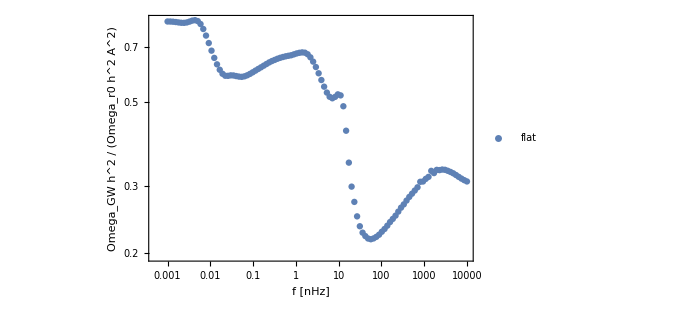

```mathematica
ListLogLogPlot[{Transpose[{fList, omFlat}]}, Joined -> False, PlotRange -> All,
  Frame -> True, FrameLabel -> {"f [nHz]", "Omega_GW h^2 / (Omega_r0 h^2 A^2)"},
  PlotLegends -> {"flat", "log-normal (f*=10 nHz, sigma=0.4)"}, ImageSize -> 500]
```

```mathematica
Manipulate[
  Module[{pz = lognormalPz[fnHzToK[10^lf], sg], om},
   om = Table[omegaGW[ker["k"], phKernel[ker, pz]], {ker, kernels}];
   ListLogLogPlot[{Transpose[{fList, omFlat}], Transpose[{fList, om}]}, Joined -> True, PlotRange -> All,
    Frame -> True, FrameLabel -> {"f [nHz]", "Omega_GW h^2 / (Omega_r0 h^2 A^2)"},
    PlotLegends -> {"flat", "log-normal"}, ImageSize -> 450]],
  {{lf, 1.}, -2., 4., 0.1, Appearance -> "Labeled"}, {{sg, 0.4}, 0.1, 1.5, 0.05, Appearance -> "Labeled"},
  TrackedSymbols :> {lf, sg}]
```

## 6. Checks

The kernel tables only cover t <= 3000, so the flat spectrum is truncated at large t. Below: Omega_GW(flat) for one kernel as the upper limit t_cut is varied.

```mathematica
tCutCheck[i_] := Module[{ker = kernels[[i]], out},
   Table[Module[{m = Flatten @ Position[ker["t"], _?(# <= tc &)], kc},
     kc = <|"f" -> ker["f"], "k" -> ker["k"], "s" -> ker["s"], "t" -> ker["t"][[m]], "I2" -> ker["I2"][[m]]|>;
     {tc, omegaGW[kc["k"], phKernel[kc, flatPz]]}], {tc, {10., 30., 100., 300., 1000., 3000.}}]];
{kernels[[60]]["f"], tCutCheck[60]}
```

{6.15164,{{10.,0.508338},{30.,0.515719},{100.,0.516469},{300.,0.516517},{1000.,0.51652},{3000.,0.51652}}}

```mathematica
kernelHeatmap[i_] := Module[{ker = kernels[[i]], data},
   data = Flatten[Table[{ker["s"][[j]], Log10[ker["t"][[m]]], Log10[Max[ker["I2"][[m, j]], 10.^-30]]},
      {m, Length[ker["t"]]}, {j, Length[ker["s"]]}], 1];
   ListDensityPlot[data, PlotRange -> All, ColorFunction -> "Rainbow", PlotLegends -> Automatic,
    FrameLabel -> {"s", "log10 t"}, PlotLabel -> Style["log10 I2bar,  f = " <> ToString[ker["f"]] <> " nHz", 12], ImageSize -> 450]];
kernelHeatmap[60]
```

-Graphics-

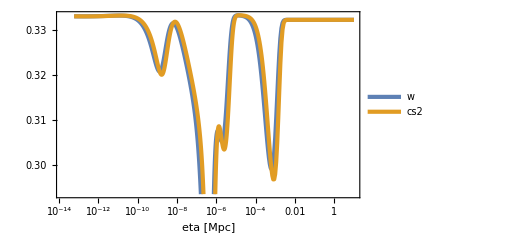
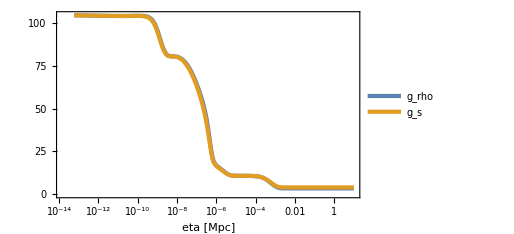

```mathematica
Row[{
  ListLogLinearPlot[{Transpose[{etaL, wL}], Transpose[{etaL, cs2L}]}, Joined -> True, Frame -> True,
   FrameLabel -> {"eta [Mpc]", ""}, PlotLegends -> {"w", "cs2"}, ImageSize -> 380],
  ListLogLinearPlot[{Transpose[{etaL, grhoL}], Transpose[{etaL, gsL}]}, Joined -> True, Frame -> True,
   FrameLabel -> {"eta [Mpc]", ""}, PlotLegends -> {"g_rho", "g_s"}, ImageSize -> 380]}, Spacer[20]]
```